# Domača naloga – Mathematica

## 1. naloga

1. Izračunajte vsoto ∑_(k=1)^30 k^2/(k+5).
2. Rešite neenačbo:|x-1|≤ 2x+3 
3. Izračunajte drugi odvod funkcije  3tg (2cos(x)+1)  sin (x) in ga poenostavite.
4. S funkcijo FindRoot numerično izračunajte ničlo funkcije  (cos(x))/(e^(x^3-1)) z začetnim približkom x = 1 .

```mathematica
Sum[k^2/k+5,{k,30}]
Reduce[Abs[x-1]<=2x+3,x]
f[x_]:= 3 Tan[2 Cos[x]+1] Sin[x]
f''[x]
FindRoot[Cos[x]/( E^x)^3-1,{x,1}]
```

615

x≥-2/3

-18 Cos[x] Sec[1+2 Cos[x]]^2 Sin[x]-3 Sin[x] Tan[1+2 Cos[x]]+24 Sec[1+2 Cos[x]]^2 Sin[x]^3 Tan[1+2 Cos[x]]

{x→4.83786×10^-18}

## 2. naloga

1. Definirajte funkciji x(t)=cos(5t) in y(t)=0.5 sin(t).
2. Poiščite take vrednosti t ∈ [0, π], da velja x(t)=0
3. Narišite parametrično podano krivuljo na območju t ∈[0,2π].

{{t→{π/10}},{t→{(3 π)/10}},{t→{π/2}},{t→{(7 π)/10}},{t→{(9 π)/10}}}

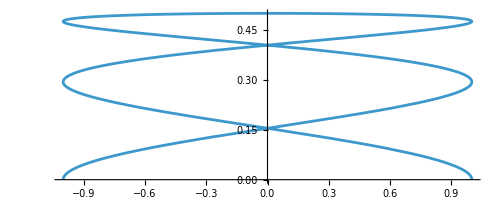

```mathematica
ClearAll[f,x]
x[t_]:=Cos[5t]
y[t_]:=0.5 Sin[t]
Solve[{x[t]==0,Element[t,Interval[{0,π}]]},t]
ParametricPlot[{x[t],y[t]},{t,0,π}]
```